## Tropical Addition

```mathematica
SetAttributes[TropicalPlus,Flat]
```

```mathematica
TropicalPlus[x_List, y_List] := MapThread[Min,{x,y}, Length[Dimensions[x]]]/;Dimensions[x]== Dimensions[y]
TropicalPlus[x_,y_]:=Min[x,y] 
Verbatim[TropicalPlus][x_]:=x
```

```mathematica
TropicalPlus[1.8, 2, 6.3]
```

1.8

```mathematica
TropicalPlus[{7,2,3,4,5},{2,3,4,5,6}]
```

{2,2,3,4,5}

```mathematica
TropicalPlus[{{1, 2}, {2, 3}, {4, 5}}, {{4, 1}, {3, 5}, {1,4}}]
```

{{1,1},{2,3},{1,4}}

## Tropical Times

```mathematica
SetAttributes[TropicalTimes,Flat]
SetAttributes[TropicalMatrixTimes,Flat]
```

```mathematica
TropicalTimes[x_,y_]:=x+y
Verbatim[TropicalTimes][x_]:=x
```

```mathematica
TropicalMatrixTimes[a_List,b_List]:=Inner[Plus,a,b,Min]
Verbatim[TropicalMatrixTimes][x_List]:=x
```

```mathematica
TropicalMatrixSquare[a_List]:=Inner[Plus,a,a,Min]
```

```mathematica
TropicalMatrixTimes[a_,b_List]:=a+b
```

```mathematica
TropicalTimes[3.2, 4]
```

7.2

```mathematica
TropicalMatrixTimes[{{0.8,2.6, 4.9}, {Infinity, 0, 2}, {1, 4.5, 0}}, {{0,2.7, 4}, {Infinity, 0.7, 2}, {1, 4.4, 0}}]
```

{{0.8,3.3,4.6},{3,0.7,2},{1,3.7,0}}

```mathematica
TropicalMatrixSquare[{{1, 2}, {5, -1}}]
```

{{2,1},{4,-2}}

```mathematica
TropicalMatrixTimes[2, {1, 2, 3}]
```

{3,4,5}

## Trivial Tropical Functions

Identity matrix

```mathematica
TropicalIdentityMatrix[n_Integer]:=IdentityMatrix[n]/.{1->0,0->Infinity}
```

```mathematica
TropicalIdentityMatrix[6]
```

{{0,∞,∞,∞,∞,∞},{∞,0,∞,∞,∞,∞},{∞,∞,0,∞,∞,∞},{∞,∞,∞,0,∞,∞},{∞,∞,∞,∞,0,∞},{∞,∞,∞,∞,∞,0}}

Tropical transpose

```mathematica
TropicalTranspose[a_List] := Transpose[a]
```

```mathematica
TropicalTranspose[{{3,5,4,7, 3.5},{-1,1,3,-2, -4.7},{1,2,0,-3, 0.5},{5,6,5.8, 3,4}}]
```

{{3,-1,1,5},{5,1,2,6},{4,3,0,5.8},{7,-2,-3,3},{3.5,-4.7,0.5,4}}

#### Constant Matrix

```mathematica
TropicalConstantMatrixQ[a_List] := If[First[Counts[Flatten[a]]] == Length[Flatten[a]], True, False]
```

```mathematica
TropicalConstantMatrixQ[{{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}]
```

False

```mathematica
TropicalConstantMatrixQ[{{1, 1}, {1, 1}, {1, 1}}]
```

True

## Tropical Determinant

```mathematica
TropicalDeterminant[a_List]:= With[{n = First[Dimensions[a]]}, 
Min[Total[Table[Extract[a, Thread[{Range[n], perm}]], {perm, Permutations[Range[n]]}], {2}]]]/;SquareMatrixQ[a] == True
```

```mathematica
TropicalDeterminant[{{3,5,4,7},{-1,1,3,-2},{1,2,0,-3},{5,6,3,4}}]
```

4

## Tropical Singularity

```mathematica
TropicalSingularQ[a_List]  := With[{terms=Table[Extract[a, Thread[{Range[First[Dimensions[a]]], perm}]], {perm, Permutations[Range[First[Dimensions[a]]]]}]}, 
If[First[Counts[Sort[Total[terms, {2}]]]] > 1 , True, False]]/;SquareMatrixQ[a] == True
```

```mathematica
TropicalSingularQ[{{1, 1, 1}, {1, 0, 1}, {1, 0, 0}}]
```

False

```mathematica
TropicalSingularQ[{{2, 7, 7}, {1, 3, -2}, {1, 3, -2}}]
```

True

## Tropical Rank of Matrix

```mathematica
TropicalRank[a_List] :=
(
r = First[Dimensions[a]];
minor= Table[Flatten[Minors[a,i,Identity],1], {i, r}];
While[AllTrue[minor[[r]],TropicalSingularQ], r--];
r
)/;SquareMatrixQ[a] == True
```

```mathematica
TropicalRank[{{0, 0, 1, 5}, {0, 0, 1, 5}, {3, 2, 2, 0}, {2, 1, 0, 2}}]
```

3

## Tropical Exponentiation

```mathematica
TropicalExp[a_, n_] := n a
```

```mathematica
TropicalMatrixExp[a_List,n_Integer]:= If[n==1, a+1]/; n<2
TropicalMatrixExp[a_List,n_Integer]:=Nest[TropicalMatrixSquare,a,n/2]/;EvenQ[n]
TropicalMatrixExp[a_List,n_Integer]:=TropicalMatrixTimes[Nest[TropicalMatrixSquare, a, (n-1)/2], a]/;OddQ[n]
```

## Tropical Polynomials

### x = Matrix

```mathematica
TropicalPolynomial[p_List, x_List] := ( n = First[Dimensions[x]];
temp = First[p]+TropicalIdentityMatrix[n];
For[i=0, i<Length[p], i++, 
temp = TropicalPlus[TropicalMatrixTimes[(temp), x], (p[[i+1]]+TropicalIdentityMatrix[n])];];
temp
)
```

### x = Integer

```mathematica
f[a_,b_] := tropicalPlus[tropicalTimes[a, x],b]
TropicalPolynomial[p_List, x_] :=  Fold[ f, p]/.{tropicalPlus->Min,tropicalTimes->Plus}
```

```mathematica
TropicalPolynomial[{1, 1}, {{1,2},{3, 4}}]
```

{{1,3},{4,1}}

```mathematica
TropicalPolynomial[{1, 2, 3}, 4]
```

3

## Polynomial Multiplication

```mathematica
TropicalPolynomialTimes[a_, b_, x_] := Expand[a*b]/. {Plus -> Min, Times -> Plus, x^n_->n*x}
```

```mathematica
TropicalPolynomialTimes[( a1*x^2 + b1*x + c1), (a2*x^2 + b2*x + c2), x]
```

Min[c1+c2,b2+c1+x,b1+c2+x,b1+b2+2 x,a2+c1+2 x,a1+c2+2 x,a2+b1+3 x,a1+b2+3 x,a1+a2+4 x]

## Tropical Adjoint of a matrix

```mathematica
TropicalAdjointMatrix[a_List] := With[{n = First[Dimensions[a]], m = Minors[a/.{Infinity -> w},First[Dimensions[a]]-1,Identity]}, 
Transpose[Partition[ TropicalDeterminant/@( Flatten[Reverse[Reverse[m, n-1]], 1]/. {w -> Infinity}), n]]]/;SquareMatrixQ[a] == True
```

```mathematica
TropicalAdjointMatrix[{{1, 0, Infinity}, {3, 4, Infinity}, {Infinity, Infinity, 1}}]
```

{{5,1,∞},{4,2,∞},{∞,∞,3}}

## Tropical Pseudo Inverse of a matrix

```mathematica
TropicalMatrixInverse[a_List] := TropicalAdjointMatrix[a]-TropicalDeterminant[a]/;SquareMatrixQ[a] == True
```

```mathematica
TropicalMatrixInverse[{{1, 0, Infinity}, {3, 4, Infinity}, {Infinity, Infinity, 1}}]
```

{{1,-3,∞},{0,-2,∞},{∞,∞,-1}}

## Power Method for computing eigen value and eigen vector of a matrix

### Get Eigen Value Data

```mathematica
GetEigenvalueData[a_List]:=Module[{isConstantMatrix,x,k,j,i,c,p,λ,listX={}},
isConstantMatrix=False; 
x[0] = TropicalIdentityMatrix[Length[a]][[All, 1]];
k= 0;
While[!isConstantMatrix,
(x[k+1]=TropicalMatrixTimes[a,x[k]];
For[j=0,j≤k,j++,
If[TropicalConstantMatrixQ[x[k+1]-x[j]],
isConstantMatrix=True;
c=x[k+1]-x[j];
p=k+1-j;]
];
k++;)
];
For[i=0,i≤k,i++,
listX=Append[listX,x[i]]
];
k=k-p;
λ = N[c[[1]]/p];
{{c[[1]],p,k,λ},listX}
]
```

### Eigen Value

```mathematica
TropicalEigenValue[a_List] :=GetEigenvalueData[a][[1,4]]
```

### Eigen Vector

```mathematica
TropicalEigenVector[a_List] := Module[{eigenvalueData={},listX={},λ,p,k,t}, 
eigenvalueData=GetEigenvalueData[a];
λ=eigenvalueData[[1,4]];
k=eigenvalueData[[1,3]];
p=eigenvalueData[[1,2]];
listX=eigenvalueData[[2]];
t=First[Transpose[TropicalIdentityMatrix[Length[a]]]]/. 0->Infinity;
For[j= 1, j≤p, j++, 
t = TropicalPlus[TropicalMatrixTimes[TropicalExp[λ, p-j], listX[[k+j-1]]], t];];
t
]
```

```mathematica
GetEigenvalueData[{{Infinity, 5, Infinity, Infinity, Infinity}, {Infinity, Infinity, 3, Infinity,2}, {4, Infinity, Infinity, Infinity, Infinity}, {Infinity, Infinity, 3, Infinity, 2}, {Infinity, Infinity, Infinity, 1, Infinity}}]
```

{{3,2,6,1.5},{{0,∞,∞,∞,∞},{∞,∞,4,∞,∞},{∞,7,∞,7,∞},{12,∞,∞,∞,8},{∞,10,16,10,∞},{15,19,∞,19,11},{24,13,19,13,20},{18,22,28,22,14},{27,16,22,16,23}}}

```mathematica
TropicalEigenValue[{{Infinity, 5, Infinity, Infinity, Infinity}, {Infinity, Infinity, 3, Infinity,2}, {4, Infinity, Infinity, Infinity, Infinity}, {Infinity, Infinity, 3, Infinity, 2}, {Infinity, Infinity, Infinity, 1, Infinity}}]
```

1.5

```mathematica
TropicalEigenVector[{{Infinity, 5, Infinity, Infinity, Infinity}, {Infinity, Infinity, 3, Infinity,2}, {4, Infinity, Infinity, Infinity, Infinity}, {Infinity, Infinity, 3, Infinity, 2}, {Infinity, Infinity, Infinity, 1, Infinity}}]
```

{16.5,13.,19.,13.,12.5}

## Applications

1. Shortest path using Tropical Algebra

Given a directed graph G = {V, E} of n vertices and a transition cost matrix C ∈ ℝ_nxn where C_ij = weight of the edge (i, j). 
In tropical algebra, (C^m)_ijis the minimum cost of moving from vertex i to vertex j in at most m steps.

Note: If all the elements in the cost matrix are positive, then C^m = C^2 for m ≥ 2, since any trip of size 3 or more steps contains a circuit.

### Graphs with non negative weights

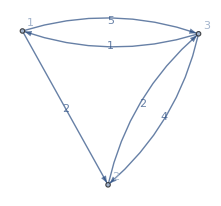

```mathematica
G = Graph[{1-> 2,1-> 3, 2 -> 3, 3-> 1, 3-> 2 }, EdgeWeight-> {2, 5, 2, 1, 4}, VertexLabels->Automatic, EdgeLabels-> "EdgeWeight"]
```

```mathematica
c = {{0, 2, 5}, {Infinity, 0, 2}, {1, 4, 0}}
```

{{0,2,5},{∞,0,2},{1,4,0}}

```mathematica
TropicalMatrixSquare[c]//MatrixForm
```

(0 | 2 | 4
3 | 0 | 2
1 | 3 | 0)

```mathematica
TropicalMatrixExp[c, 100]//MatrixForm
```

(0 | 2 | 4
3 | 0 | 2
1 | 3 | 0)

### Graphs with negative weights

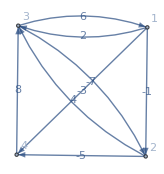

```mathematica
G = Graph[{1-> 2,1-> 3,1-> 4, 2 -> 3, 2-> 4, 3-> 1, 3-> 2 , 4-> 3}, EdgeWeight-> {-1, 2, -3, 4, -5, 6, -7, 8}, VertexLabels->Automatic, EdgeLabels->"EdgeWeight"]
```

```mathematica
c = {{0, -1, 2, -3}, {Infinity, 0, 4, -5}, {6, -7, 0, Infinity}, {Infinity, Infinity, 8, 0}}
```

{{0,-1,2,-3},{∞,0,4,-5},{6,-7,0,∞},{∞,∞,8,0}}

```mathematica
TropicalMatrixExp[c, 10]//MatrixForm
```

(-37 | -50 | -44 | -53
-35 | -48 | -42 | -51
-40 | -53 | -48 | -57
-31 | -44 | -38 | -47)

```mathematica
TropicalMatrixExp[c, 3]//MatrixForm
```

(0 | -5 | -1 | -10
9 | -4 | 1 | -8
3 | -10 | -4 | -12
14 | 1 | 5 | -4)

```mathematica
2. Key Generation for a cryptosystem
```

Let R be the tropical algebra of n × n matrices over integers

Let n be the size of public key matrices A and B:

```mathematica
n= 10;
```

let A, B ∈ R be public matrices such that A ⊗ B  ≠  B ⊗ A:

```mathematica
A= RandomInteger[{-10^10,10^10},{10, 10}];
B= RandomInteger[{-10^10,10^10},{10, 10}];
```

Now p1 and p2 are random polynomials selected by Alice:

```mathematica
p1= RandomInteger[{-1000, 1000}, n];
p2 = RandomInteger[{-1000, 1000}, n];
```

Alice computes the values of p1 and p2 for A and B respectively:

```mathematica
p1A = TropicalPolynomial[p1, A];
p2B = TropicalPolynomial[p2, B];
```

Alice sends the tropical product of these two matrices and sends to Bob:

```mathematica
p = TropicalMatrixTimes[p1A, p2B];
```

Now q1 and q2 are random polynomials selected by Bob:

```mathematica
q1 = RandomInteger[{-1000, 1000}, n];
q2 = RandomInteger[{-1000, 1000}, n];
```

Now q1A and q2B are values of polynomials q1 and q2 at A and B respectively:

```mathematica
q1A = TropicalPolynomial[q1, A];
q2B = TropicalPolynomial[q2, B];
```

Bob sends the tropical product of these two matrices to Alice:

```mathematica
q = TropicalMatrixTimes[q1A, q2B];
```

Now if Alice computes p1A⊗q⊗p2B and Bob computes q1A⊗p⊗q2B:

```mathematica
keyA = TropicalMatrixTimes[TropicalMatrixTimes[p1A, q], p2B];
keyB = TropicalMatrixTimes[TropicalMatrixTimes[q1A, p], q2B];
```

We notice that the value of keyA and keyB is same:

```mathematica
keyA == keyB
```

True

Let key = keyA = keyB:

```mathematica
key = keyA;
```

Hence key = keyA = keyB can be used for encryption.

### Parameters for key generation

• The size n of matrices A and B  = 10.
• The entries of the public matrices A, B are integers, selected uniformly randomly in the range [−10^10 , 10^10].
• The degrees of the tropical polynomials p1, p2, q1, q2 are selected uniformly randomly in the range [1, 10].
• The coefficients of the above tropical polynomials are selected uniformly randomly in the range [−1000, 1000].

With these parameters, the size of the key space (for private tropical polynomials) is approximately 10^30